# Test: SubPixelFit library

Aims: 
1) create tests for (a) accuracy, (b) speed and (c) error handling 
2) Create testing cases:
	2.a) Symmetric gaussian particles + noise
	2.b) Non-symmetric gaussian particles + noise
	2.c) Real practice images (500nm) particles
	2.d) Special cases with possible errors

Specifications:

## Tracking function

input: image with background substracted
output: {x,y, confidence, size (optional), angle (optional), flattening(optional)}

## Laoding Tools

```mathematica
(*get key library - namy parts of this code might need to be overwritten for testing*)
Import @ FileNameJoin@{DirectoryName[NotebookDirectory[] ], "bin/packages/SubPixelFit.m"}
```

#### Generate testing data set (2.a)

```mathematica
GenerateGaussianParticle[box_, μ_, size_:10.0, θ_:0, flattening_:0, noise_:0.03] := 
Block[{data,a,b,c, σx,σy, dist, x,y,var},
σx = size √(1-flattening); (*preserve area of 'size' particle*)
σy = size/√(1-flattening);
a = Cos[θ]^2/(2 σx^2) + Sin[θ]^2/(2 σy^2) //N;
b= (-Sin[2θ])/(4 σx^2) + Sin[2θ]/(4 σy^2)//N;
c = Sin[θ]^2/(2 σx^2) + Cos[θ]^2/(2 σy^2)//N;
var = Inverse@{{a,b},{b,c}};
dist = 2π Det[var]^(1/2)  PDF[ MultinormalDistribution[Reverse@μ+{0.5,0.5}, var],{x,y}];
data = Round[  255 Table[ dist, {x,1,box}, {y,1,box}] ];
(*Print["σx"-> σx];
Print["matrix"->  {{a,b},{b,c}}];
Print["dist"->  dist//Simplify];*)
(ImageReflect@Image[data, "Byte"]) ~ ImageEffect ~ {"GaussianNoise",noise}
]
```

```mathematica
Manipulate[Show[GenerateGaussianParticle[20,{x,y}, size, angle, flt, 0.02], ImageSize-> Small], {angle, 0, Pi}, {{size,2}, 0.2, 4}, {{x,10},-10,30}, {{y,10},0,20}, {{flt,0.5},0,0.9}]
```

```mathematica
(*output: list of {image, position, size, angle, flattening}*)
GenerateTestDataSet[n_, box_, sizeRange_, flatteningRange_:{0,0}]:= Module[
{results,posRange, randomPos},
posRange[size_] := {0, box} + {1,-1} * 1.5 size;
randomPos[posRange_] := {RandomReal@posRange, RandomReal@posRange};
results =  Table[{{}, {}, RandomReal@sizeRange, RandomReal@{0, Pi},RandomReal@flatteningRange} , {i, n}];
results⟦All, 2⟧ = randomPos/@posRange /@ results⟦All, 3⟧;
results⟦All, 1⟧ = GenerateGaussianParticle[box, #⟦2⟧,#⟦3⟧, #⟦4⟧, #⟦5⟧] &/@ results;
results
]
```

```mathematica
(*multiple images close by*)
GenerateTestDataSetTwoParticles[n_, box_, sizeRange_, flatteningRange_, separationRange_]:= 
Module[ {results, posRange, randomPos, secondPos, secondParticle},
posRange[size_] := {0, box} + {1,-1} * 1.8 size;
randomPos[posRange_] := {RandomReal@posRange, RandomReal@posRange};
results =  Table[{{}, {}, RandomReal@sizeRange, RandomReal@{0, Pi},RandomReal@flatteningRange} , {i, n}];
results⟦All, 2⟧ = randomPos /@ posRange /@ results⟦All, 3⟧;
results⟦All, 1⟧ = GenerateGaussianParticle[box, #⟦2⟧,#⟦3⟧, #⟦4⟧, #⟦5⟧] &/@ results;
(*generate another image for second partile*)
secondPos[fisrtPos_] := fisrtPos + RandomReal[ separationRange ]*{Cos[#], Sin[#]} &@RandomReal[{0,2 Pi}];
secondParticle = GenerateGaussianParticle[box, #, Mean@sizeRange, 0,0] &/@ (secondPos /@ results⟦All, 2⟧);
results⟦All, 1⟧ = MapThread[ ImageAdd,  { results⟦All, 1⟧, secondParticle} ];
results
]
```

#### Assesment tools

Want to know:
1) time it took the function
2) Accuracy in X fit
3) Accuracy in Y fit
4) Drop rate (accuracy paramter <0.75)
5) Size estimate - relative is enough, check how linear it is (correlation coefficient?) 
6) angle - range {0, π} 
7) flattening - relative is enough

Estimator should include typical error, but penalise large errors thus something along the lines of √⟨(X - μ)^2⟩

```mathematica
(*return all results as listed above*)
AssesFunction[name_,fn_, testSet_]:= Module[
{foundSet, time,accuracyPos, correlationSize, accuracyAngle, correlationFlattening, dropRate},

{time, foundSet} = AbsoluteTiming[ fn/@ testSet⟦All, 1⟧ ];
accuracyPos =  Sqrt@Mean@Transpose@((foundSet⟦All, {1,2}⟧ - testSet⟦All, 2⟧)^2);
(*alternative*)
(*accuracyPos =  Mean@Abs@Transpose@(foundSet⟦All, {1,2}⟧ - dataSet⟦All, 2⟧);*)
dropRate = N[ Count[foundSet⟦All, 3⟧,_?(#<0.75&)] / Length@testSet];
correlationSize = If[ Length@First@foundSet <4, "-",
Correlation[testSet⟦All, 3⟧, foundSet⟦All, 4⟧]    ];
accuracyAngle = If[ Length@First@foundSet <5, "-",
180.0/Pi *Mean@((Min@Abs@{#, #-Pi}&)/@(testSet⟦All, 4⟧- foundSet⟦All, 5⟧)) ];
correlationFlattening = If[ Length@First@foundSet <6, "-",
Correlation[testSet⟦All, 5⟧, foundSet⟦All, 6⟧]    ];
<|"Name"-> name,
"Time"->  time, 
"√⟨SuperscriptBox[Δx, 2]⟩"-> accuracyPos⟦1⟧,
 "√⟨SuperscriptBox[Δy, 2]⟩"-> accuracyPos⟦2⟧,
"Drop Rate" -> dropRate,
"ρ(size)"-> correlationSize, 
"⟨|Δα|⟩"-> accuracyAngle,
"ρ(f)"-> correlationFlattening|>
]
```

## Generate training sets

#### Gaussian Particles (esay)

```mathematica
testSet = GenerateTestDataSet[1000, 6, {1.6,1.7}, {0.05,0.08}];
testSet⟦;;10, 1⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Real images (todo)

#### Multiple particles (todo)

```mathematica
testSet =GenerateTestDataSetTwoParticles[1000, 8, {1.2,1.3}, {0.0,0.0}, {5,7}];
testSet⟦;;20, 1⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Run Test

```mathematica
Dataset[{
AssesFunction["Centroid (built in)", Centroid, testSet],
AssesFunction["CentroidCustom", CentroidCustom, testSet],
(*AssesFunction["SPFCentroidWithProperties", SPFCentroidWithProperties, testSet],*)
AssesFunction["SPFCentroidWithProperties2", SPFCentroidWithProperties2, testSet],
AssesFunction["SPFGaussian", SPFGaussian, testSet],
AssesFunction["SPFGaussianOptimised", SPFGaussianOptimised, testSet],
AssesFunction["SPFGaussianVarianceMatrix", SPFGaussianVarianceMatrix, testSet],
AssesFunction["SPFGaussianFixedAngle", SPFGaussianFixedAngle, testSet],
AssesFunction["SPFGaussianFixed", SPFGaussianFixed, testSet],
AssesFunction["SubPixel2DGaussianFixedFit (old)", SubPixel2DGaussianFixedFit, testSet]
}]
```

#### Look at detailed deviations

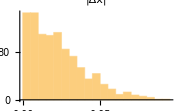
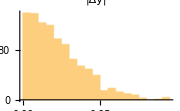

```mathematica
method = (SPFGaussianOptimisedV2@#&);
foundSet = method/@ testSet⟦All, 1⟧ ; 
dPos = Abs@(foundSet⟦All, {1,2}⟧ - testSet⟦All, 2⟧);
Row@{Histogram[dPos⟦All,1⟧, ImageSize->Small, PlotLabel->"|Δx|"], Histogram[dPos⟦All,2⟧, ImageSize->Small, PlotLabel->"|Δy|"]}
```

```mathematica
angles = Transpose@{ testSet⟦All,4⟧, foundSet⟦All,5⟧}*180/Pi;
```

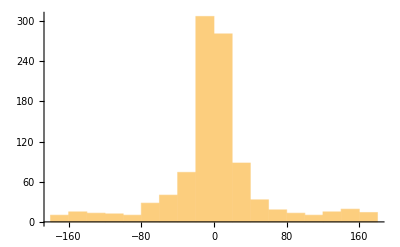

```mathematica
Histogram[ (angles⟦All,1⟧ - angles⟦All,2⟧)]
```

```mathematica
angles⟦;;20⟧
```

#### Overlay point of detection

```mathematica
ShowPosOverlayed[testRow_,fn_]:=Block[{pos, img = testRow⟦1⟧},
pos = (fn@img)⟦{1,2}⟧;
Print["pos" -> pos];
Show[img,Graphics@Flatten@{Green,Point[testRow⟦2⟧],Red,Point[pos]}, ImageSize -> Small]
]
```

pos→{1.98322,2.47979}

pos→{2.60958,4.4582}

pos→{4.78019,2.35894}

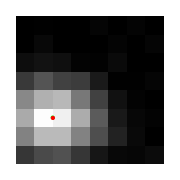
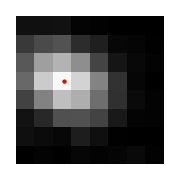
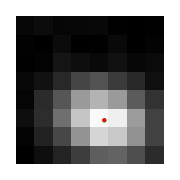

```mathematica
ShowPosOverlayed[#, SPFGaussian]&/@testSet⟦;;3⟧
```

```mathematica
t =-Graphics-;
```

```mathematica
Binarize@t
```

-Graphics-

```mathematica
ComponentMeasurements[ Binarize@t, "BoundingBox"]
```

{1→{{0.,0.},{6.,5.}}}

```mathematica
ImageTrim[t, {{-1,-2},{20.,4.}}]
```

-Graphics-

```mathematica
Min[-1, 8]
```

-1